```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
PtsBase=(Import["Profile_file_plas_520.txt","Table"][[4;;-7]])[[All,{2,3}]]
```

{{0.5,0},{0.499239,0.00382683},{0.497071,0.00707107},{0.493827,0.0092388},{0.49,0.01},{0.486111,0.01},{0.482222,0.01},{0.478333,0.01},{0.474444,0.01},{0.470556,0.01},{0.466667,0.01},{0.462778,0.01},{0.458889,0.01},{0.455,0.01},{0.451111,0.01},{0.447222,0.01},{0.443333,0.01},{0.439444,0.01},{0.435556,0.01},{0.431667,0.01},{0.427778,0.01},{0.423889,0.01},{0.42,0.01},{0.416111,0.01},{0.412222,0.01},{0.408333,0.01},{0.404444,0.01},{0.400556,0.01},{0.396667,0.01},{0.392778,0.01},{0.388889,0.01},{0.385,0.01},{0.381111,0.01},{0.377222,0.01},{0.373333,0.01},{0.369444,0.01},{0.365556,0.01},{0.361667,0.01},{0.357778,0.01},{0.353889,0.01},{0.35,0.01},{0.346111,0.01},{0.342222,0.01},{0.338333,0.01},{0.334444,0.01},{0.330556,0.01},{0.326667,0.01},{0.322778,0.01},{0.318889,0.01},{0.315,0.01},{0.311111,0.01},{0.307222,0.01},{0.303333,0.01},{0.299444,0.01},{0.295556,0.01},{0.291667,0.01},{0.287778,0.01},{0.283889,0.01},{0.28,0.01},{0.276111,0.01},{0.272222,0.01},{0.268333,0.01},{0.264444,0.01},{0.260556,0.01},{0.256667,0.01},{0.252778,0.01},{0.248889,0.01},{0.245,0.01},{0.241111,0.01},{0.237222,0.01},{0.233333,0.01},{0.229444,0.01},{0.225556,0.01},{0.221667,0.01},{0.217778,0.01},{0.213889,0.01},{0.21,0.01},{0.206111,0.01},{0.202222,0.01},{0.198333,0.01},{0.194444,0.01},{0.190556,0.01},{0.186667,0.01},{0.182778,0.01},{0.178889,0.01},{0.175,0.01},{0.171111,0.01},{0.167222,0.01},{0.163333,0.01},{0.159444,0.01},{0.155556,0.01},{0.151667,0.01},{0.147778,0.01},{0.143889,0.01},{0.14,0.01},{0.136111,0.01},{0.132222,0.01},{0.128333,0.01},{0.124444,0.01},{0.120556,0.01},{0.116667,0.01},{0.112778,0.01},{0.108889,0.01},{0.105,0.01},{0.101111,0.01},{0.0972222,0.01},{0.0933333,0.01},{0.0894444,0.01},{0.0855556,0.01},{0.0816667,0.01},{0.0777778,0.01},{0.0738889,0.01},{0.07,0.01},{0.0661111,0.01},{0.0622222,0.01},{0.0583333,0.01},{0.0544444,0.01},{0.0505556,0.01},{0.0466667,0.01},{0.0427778,0.01},{0.0388889,0.01},{0.035,0.01},{0.0311111,0.01},{0.0272222,0.01},{0.0233333,0.01},{0.0194444,0.01},{0.0155556,0.01},{0.0116667,0.01},{0.00777778,0.01},{0.00388889,0.01},{0,0.01},{-0.00388889,0.01},{-0.00777778,0.01},{-0.0116667,0.01},{-0.0155556,0.01},{-0.0194444,0.01},{-0.0233333,0.01},{-0.0272222,0.01},{-0.0311111,0.01},{-0.035,0.01},{-0.0388889,0.01},{-0.0427778,0.01},{-0.0466667,0.01},{-0.0505556,0.01},{-0.0544444,0.01},{-0.0583333,0.01},{-0.0622222,0.01},{-0.0661111,0.01},{-0.07,0.01},{-0.0738889,0.01},{-0.0777778,0.01},{-0.0816667,0.01},{-0.0855556,0.01},{-0.0894444,0.01},{-0.0933333,0.01},{-0.0972222,0.01},{-0.101111,0.01},{-0.105,0.01},{-0.108889,0.01},{-0.112778,0.01},{-0.116667,0.01},{-0.120556,0.01},{-0.124444,0.01},{-0.128333,0.01},{-0.132222,0.01},{-0.136111,0.01},{-0.14,0.01},{-0.143889,0.01},{-0.147778,0.01},{-0.151667,0.01},{-0.155556,0.01},{-0.159444,0.01},{-0.163333,0.01},{-0.167222,0.01},{-0.171111,0.01},{-0.175,0.01},{-0.178889,0.01},{-0.182778,0.01},{-0.186667,0.01},{-0.190556,0.01},{-0.194444,0.01},{-0.198333,0.01},{-0.202222,0.01},{-0.206111,0.01},{-0.21,0.01},{-0.213889,0.01},{-0.217778,0.01},{-0.221667,0.01},{-0.225556,0.01},{-0.229444,0.01},{-0.233333,0.01},{-0.237222,0.01},{-0.241111,0.01},{-0.245,0.01},{-0.248889,0.01},{-0.252778,0.01},{-0.256667,0.01},{-0.260556,0.01},{-0.264444,0.01},{-0.268333,0.01},{-0.272222,0.01},{-0.276111,0.01},{-0.28,0.01},{-0.283889,0.01},{-0.287778,0.01},{-0.291667,0.01},{-0.295556,0.01},{-0.299444,0.01},{-0.303333,0.01},{-0.307222,0.01},{-0.311111,0.01},{-0.315,0.01},{-0.318889,0.01},{-0.322778,0.01},{-0.326667,0.01},{-0.330556,0.01},{-0.334444,0.01},{-0.338333,0.01},{-0.342222,0.01},{-0.346111,0.01},{-0.35,0.01},{-0.353889,0.01},{-0.357778,0.01},{-0.361667,0.01},{-0.365556,0.01},{-0.369444,0.01},{-0.373333,0.01},{-0.377222,0.01},{-0.381111,0.01},{-0.385,0.01},{-0.388889,0.01},{-0.392778,0.01},{-0.396667,0.01},{-0.400556,0.01},{-0.404444,0.01},{-0.408333,0.01},{-0.412222,0.01},{-0.416111,0.01},{-0.42,0.01},{-0.423889,0.01},{-0.427778,0.01},{-0.431667,0.01},{-0.435556,0.01},{-0.439444,0.01},{-0.443333,0.01},{-0.447222,0.01},{-0.451111,0.01},{-0.455,0.01},{-0.458889,0.01},{-0.462778,0.01},{-0.466667,0.01},{-0.470556,0.01},{-0.474444,0.01},{-0.478333,0.01},{-0.482222,0.01},{-0.486111,0.01},{-0.49,0.01},{-0.493827,0.0092388},{-0.497071,0.00707107},{-0.499239,0.00382683},{-0.5,0},{-0.499239,-0.00382683},{-0.497071,-0.00707107},{-0.493827,-0.0092388},{-0.49,-0.01},{-0.486111,-0.01},{-0.482222,-0.01},{-0.478333,-0.01},{-0.474444,-0.01},{-0.470556,-0.01},{-0.466667,-0.01},{-0.462778,-0.01},{-0.458889,-0.01},{-0.455,-0.01},{-0.451111,-0.01},{-0.447222,-0.01},{-0.443333,-0.01},{-0.439444,-0.01},{-0.435556,-0.01},{-0.431667,-0.01},{-0.427778,-0.01},{-0.423889,-0.01},{-0.42,-0.01},{-0.416111,-0.01},{-0.412222,-0.01},{-0.408333,-0.01},{-0.404444,-0.01},{-0.400556,-0.01},{-0.396667,-0.01},{-0.392778,-0.01},{-0.388889,-0.01},{-0.385,-0.01},{-0.381111,-0.01},{-0.377222,-0.01},{-0.373333,-0.01},{-0.369444,-0.01},{-0.365556,-0.01},{-0.361667,-0.01},{-0.357778,-0.01},{-0.353889,-0.01},{-0.35,-0.01},{-0.346111,-0.01},{-0.342222,-0.01},{-0.338333,-0.01},{-0.334444,-0.01},{-0.330556,-0.01},{-0.326667,-0.01},{-0.322778,-0.01},{-0.318889,-0.01},{-0.315,-0.01},{-0.311111,-0.01},{-0.307222,-0.01},{-0.303333,-0.01},{-0.299444,-0.01},{-0.295556,-0.01},{-0.291667,-0.01},{-0.287778,-0.01},{-0.283889,-0.01},{-0.28,-0.01},{-0.276111,-0.01},{-0.272222,-0.01},{-0.268333,-0.01},{-0.264444,-0.01},{-0.260556,-0.01},{-0.256667,-0.01},{-0.252778,-0.01},{-0.248889,-0.01},{-0.245,-0.01},{-0.241111,-0.01},{-0.237222,-0.01},{-0.233333,-0.01},{-0.229444,-0.01},{-0.225556,-0.01},{-0.221667,-0.01},{-0.217778,-0.01},{-0.213889,-0.01},{-0.21,-0.01},{-0.206111,-0.01},{-0.202222,-0.01},{-0.198333,-0.01},{-0.194444,-0.01},{-0.190556,-0.01},{-0.186667,-0.01},{-0.182778,-0.01},{-0.178889,-0.01},{-0.175,-0.01},{-0.171111,-0.01},{-0.167222,-0.01},{-0.163333,-0.01},{-0.159444,-0.01},{-0.155556,-0.01},{-0.151667,-0.01},{-0.147778,-0.01},{-0.143889,-0.01},{-0.14,-0.01},{-0.136111,-0.01},{-0.132222,-0.01},{-0.128333,-0.01},{-0.124444,-0.01},{-0.120556,-0.01},{-0.116667,-0.01},{-0.112778,-0.01},{-0.108889,-0.01},{-0.105,-0.01},{-0.101111,-0.01},{-0.0972222,-0.01},{-0.0933333,-0.01},{-0.0894444,-0.01},{-0.0855556,-0.01},{-0.0816667,-0.01},{-0.0777778,-0.01},{-0.0738889,-0.01},{-0.07,-0.01},{-0.0661111,-0.01},{-0.0622222,-0.01},{-0.0583333,-0.01},{-0.0544444,-0.01},{-0.0505556,-0.01},{-0.0466667,-0.01},{-0.0427778,-0.01},{-0.0388889,-0.01},{-0.035,-0.01},{-0.0311111,-0.01},{-0.0272222,-0.01},{-0.0233333,-0.01},{-0.0194444,-0.01},{-0.0155556,-0.01},{-0.0116667,-0.01},{-0.00777778,-0.01},{-0.00388889,-0.01},{0,-0.01},{0.00388889,-0.01},{0.00777778,-0.01},{0.0116667,-0.01},{0.0155556,-0.01},{0.0194444,-0.01},{0.0233333,-0.01},{0.0272222,-0.01},{0.0311111,-0.01},{0.035,-0.01},{0.0388889,-0.01},{0.0427778,-0.01},{0.0466667,-0.01},{0.0505556,-0.01},{0.0544444,-0.01},{0.0583333,-0.01},{0.0622222,-0.01},{0.0661111,-0.01},{0.07,-0.01},{0.0738889,-0.01},{0.0777778,-0.01},{0.0816667,-0.01},{0.0855556,-0.01},{0.0894444,-0.01},{0.0933333,-0.01},{0.0972222,-0.01},{0.101111,-0.01},{0.105,-0.01},{0.108889,-0.01},{0.112778,-0.01},{0.116667,-0.01},{0.120556,-0.01},{0.124444,-0.01},{0.128333,-0.01},{0.132222,-0.01},{0.136111,-0.01},{0.14,-0.01},{0.143889,-0.01},{0.147778,-0.01},{0.151667,-0.01},{0.155556,-0.01},{0.159444,-0.01},{0.163333,-0.01},{0.167222,-0.01},{0.171111,-0.01},{0.175,-0.01},{0.178889,-0.01},{0.182778,-0.01},{0.186667,-0.01},{0.190556,-0.01},{0.194444,-0.01},{0.198333,-0.01},{0.202222,-0.01},{0.206111,-0.01},{0.21,-0.01},{0.213889,-0.01},{0.217778,-0.01},{0.221667,-0.01},{0.225556,-0.01},{0.229444,-0.01},{0.233333,-0.01},{0.237222,-0.01},{0.241111,-0.01},{0.245,-0.01},{0.248889,-0.01},{0.252778,-0.01},{0.256667,-0.01},{0.260556,-0.01},{0.264444,-0.01},{0.268333,-0.01},{0.272222,-0.01},{0.276111,-0.01},{0.28,-0.01},{0.283889,-0.01},{0.287778,-0.01},{0.291667,-0.01},{0.295556,-0.01},{0.299444,-0.01},{0.303333,-0.01},{0.307222,-0.01},{0.311111,-0.01},{0.315,-0.01},{0.318889,-0.01},{0.322778,-0.01},{0.326667,-0.01},{0.330556,-0.01},{0.334444,-0.01},{0.338333,-0.01},{0.342222,-0.01},{0.346111,-0.01},{0.35,-0.01},{0.353889,-0.01},{0.357778,-0.01},{0.361667,-0.01},{0.365556,-0.01},{0.369444,-0.01},{0.373333,-0.01},{0.377222,-0.01},{0.381111,-0.01},{0.385,-0.01},{0.388889,-0.01},{0.392778,-0.01},{0.396667,-0.01},{0.400556,-0.01},{0.404444,-0.01},{0.408333,-0.01},{0.412222,-0.01},{0.416111,-0.01},{0.42,-0.01},{0.423889,-0.01},{0.427778,-0.01},{0.431667,-0.01},{0.435556,-0.01},{0.439444,-0.01},{0.443333,-0.01},{0.447222,-0.01},{0.451111,-0.01},{0.455,-0.01},{0.458889,-0.01},{0.462778,-0.01},{0.466667,-0.01},{0.470556,-0.01},{0.474444,-0.01},{0.478333,-0.01},{0.482222,-0.01},{0.486111,-0.01},{0.49,-0.01},{0.493827,-0.0092388},{0.497071,-0.00707107},{0.499239,-0.00382683}}

```mathematica
Pts=Reverse@Table[PtsBase[[q]],{q,1,Length[PtsBase],1}];
```

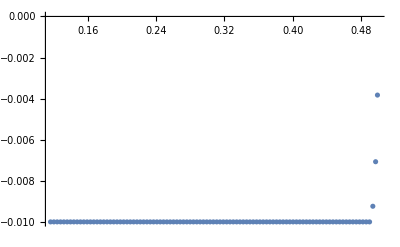

```mathematica
ListPlot[Pts[[1;;100]]]
```

```mathematica
n=Pts//Length
```

520

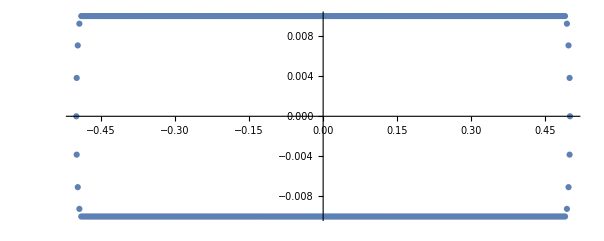

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Export["Blasius"<>ToString[n],{"#This is a textfile with points on Blasius airfoil"}~Join~{"np = "<>ToString[n]}~Join~{"r = { \\"}~Join~((ToString[#]<>", \\")&/@(Pts[[1;;-2]]))~Join~((ToString[#]<>" \\")&/@(Pts[[{-1}]]))~Join~{" }"}]
```

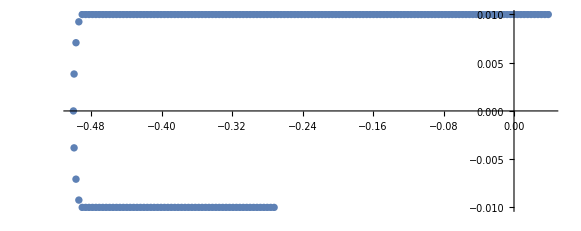

```mathematica
ListPlot[Pts[[200;;400]],AspectRatio->Automatic]
```